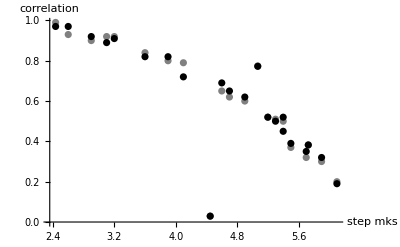

correlation : 0.27666

correlation1 : 0.277739

```mathematica
(*set1=Import["/Users/artemiyrr/Desktop/qwertyuiop1/a2 copy.csv"];
table= Import["/Users/artemiyrr/Desktop/qwertyuiop1/awertyuiop.csv"];*)


(*b=ParallelTable[set1[[z]][[p]],{z,2,Length[set1]},{p,1,2}];*)
(*ParallelTable[table[[z]]->z,{z,1,Length[set1]-1}];*)
(*AverageX=2495.4229975000053;
AverageY=2495.4229974999785;*)
(*Print[PointValuePlot[ParallelTable[b[[r]]->r,{r,1,Length[set1]-1}],PlotLabel->" в начале "]];*)
(*Print[PointValuePlot[ParallelTable[table[[z]]->z,{z,1,Length[set1]-1}],PlotLabel->" в конце "]];*)
(*Print[ListLinePlot[Table[{b[[i]],table[[i]]},{i,1,Length[b]}]]];*)
(*Print[ListPlot[Table[{table[[i]]-b[[i]]},{i,1,Length[b]}],ImageSize->Large]];*)
(*a=Total[Table[Norm[{table[[i]]-b[[i]]}],{i,1,Length[b]}]]/(Length[set1]-1);*)


X=ParallelTable[table[[i]][[1]]-set1[[i]][[1]],{i,1,Length[table]}];
Y=ParallelTable[table[[i]][[2]]-set1[[i]][[2]],{i,1,Length[table]}];


(*AverageX=Sum[X[[j]]/Length[X],{j,1,Length[X]}];*)
AverageX=238362;
(*AverageY=Sum[Y[[j]]/Length[Y],{j,1,Length[Y]}];*)
AverageY=734287;
(*μ=RandomReal[{1,10}];
σ=RandomReal[{1,10}];*)
(*aa[i_,μ_]:=  X[[i]]-Expectation[x,x\[Distributed]NormalDistribution[μ,σ]];
bb[i_,μ_]:=  Y[[i]]-Expectation[y,y\[Distributed]NormalDistribution[μ,σ]];*)
(*Max[Max[X]-Min[X],1];*)
aa[i_]:=   X[[i]]-AverageX;
bb[i_]:=  Y[[i]]-AverageY;
(*aa[i_]:=   X[[i]]- 7535.199722499998;
bb[i_]:=   Y[[i]]-7535.199722499998;*)
correlation = (Sum[aa[i]*bb[i],{i,1,Length[X]}])/(   Sqrt[Sum[(aa[i])^2,{i,1,Length[X]}]]*Sqrt[Sum[(bb[i])^2,{i,1,Length[X]}]]);
(*Print[" a : ",   correlation];*)
aa1[i_]:=X[[i]]
bb1[i_]:=Y[[i]];
correlation1 = (Sum[aa1[i]*bb1[i],{i,1,Length[X]}])/(   Sqrt[Sum[(aa1[i])^2,{i,1,Length[X]}]]*Sqrt[Sum[(bb1[i])^2,{i,1,Length[X]}]]);
(*Print[" b : ", correlation1];*)
(*Plot[{correlation*x,correlation1*x,x},{x,-10,100}]*)
Show[ListPlot[{(*{step,correlation}*){2.435517564912643,0.99},{3.1,0.92},{4.449265187470026,0.029399330657751535},{3.2,0.92},{2.6,0.93},{2.9,0.9},{3.6,0.84},{3.9,0.8},{4.1,0.79},{5.068700825605612,0.7743472602892802},{5.726973660099847,0.3818721581390393},{4.6,0.65},{4.7,0.62},{4.9,0.6},{5.2,0.52},{5.3,0.51},{5.4,0.5},{5.5,0.37},{5.7,0.32},{5.9,0.3},{6.1,0.2}},PlotStyle->Gray,PlotRange->All,AxesLabel->{"step mks","correlation"}],ListPlot[{{1.0164873982493752,0.42224844233178585},{2.435517564912643,0.97},{3.1,0.89},{3.2,0.91},{2.6,0.97},{2.9,0.92},{5.4,0.52},{4.449265187470026,0.029035062096996314},{5.068700825605612,0.7722549331644774},{5.726973660099847,0.38243096530068055},{3.6,0.82},{3.9,0.82},{4.1,0.72},{4.6,0.69},{4.7,0.65},{4.9,0.62},{5.2,0.52},{5.3,0.5},{5.4,0.45},{5.5,0.39},{5.7,0.35},{5.9,0.32},{6.1,0.19}},PlotStyle->Black,PlotRange->All,AxesLabel->{"step mks","correlation"}]]

(*Show[ListPlot[ParallelTable[{X[[i]],Y[[i]]},{i,1,Length[X]}],PlotRange->{{Min[X],Max[X]},{Min[X],Max[X]}}],Plot[{correlation*x,correlation1*x,x},{x,Min[X],Max[X]},PlotRange->{{Min[X],Max[X]},{Min[X],Max[X]}}]]*)

Print[" correlation : ",correlation]

Print[" correlation1 : ",correlation1 ]

(*Max[Y]*)
```

```mathematica
set1=Import["/Users/artemiyrr/Desktop/qwertyuiop1/a2 copy.csv"];
table= Import["/Users/artemiyrr/Desktop/qwertyuiop1/awertyuiop.csv"];ListPlot[{set1[[1]]->0,set1[[1]]+2.5->1,set1[[1]]+2->30,set1[[1]]+3->60,set1[[1]]-3->120,set1[[1]]-2->200,set1[[1]]-1->240,{set1[[1]][[1]]-1.5,set1[[1]][[2]]}->180,set1[[1]][[1]]}->180,{set1[[1]][[2]]+1.5,set1[[1]][[1]]}->180,set1[[1]][[1]]->220}]
```

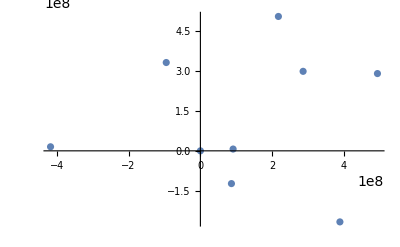

```mathematica
ListPlot[table]
```

```mathematica
{5.9,0.32},{6.1,0.3},{5.4,0.5}
```

```mathematica
set1=Import["/Users/artemiyrr/Desktop/qwertyuiop1/a2 copy.csv"];
set1[[4]][[1]]
```

-4.21853

10

step: 9.75268

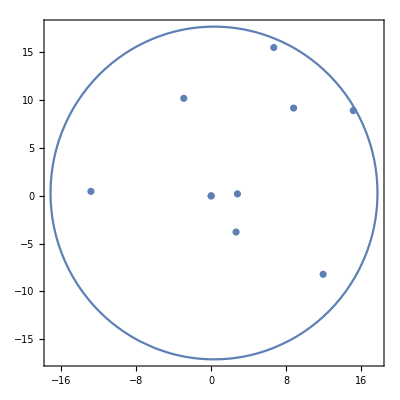

```mathematica
(*qwerty=Table[{RandomReal[{0,10^6*10^-6}],RandomReal[{0,10^6*10^-6}]},{i,0,1000}];*)
(*qwerty=Table[{i,2*i},{i,0,4}]*)

qwerty={{0,0},{0,0}};
n=9;
r=17.4;(*0.000003;*)(*0.00003*)
For[i=0,i<n,i++,x=RandomReal[{-r-0.3,r+0.3}];
y=RandomReal[{-r-0.3,r+0.3}];
If[(x-0.3)^2+(y-0.3)^2<=r^2,AppendTo[qwerty,{x,y}],Nothing]];
Export["/Users/artemiyrr/Desktop/qwertyuiop1/a2 copy.csv",qwerty];
step=Sqrt[Pi*r^2/Length[qwerty]];
Length[qwerty]
Print[" step: ",step]
Show[ContourPlot[(x-0.3)^2+(y-0.3)^2==r^2,{x,0.3-r,0.3+r},{y,0.3-r,0.3+r},PlotRange->All],ListPlot[qwerty]]
```

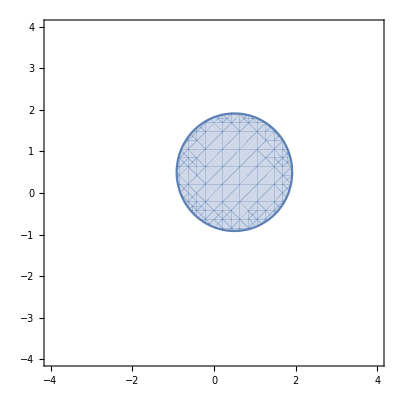

```mathematica
RegionPlot[(x-0.5)^2+(y-0.5)^2<=2,{x,-4,4},{y,-4,4}]
```

```mathematica
Print[step]
```

0.18732

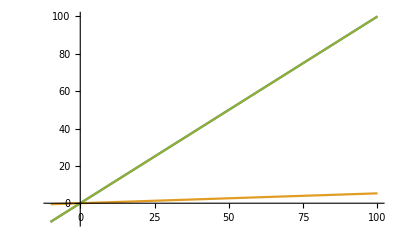
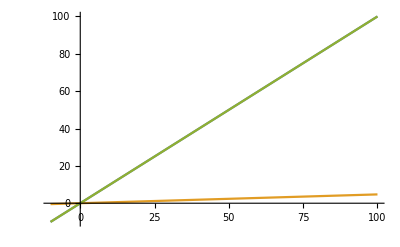
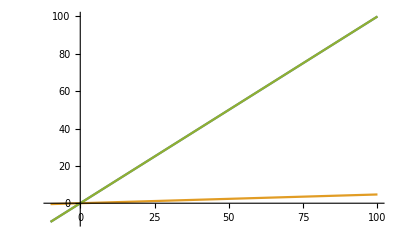
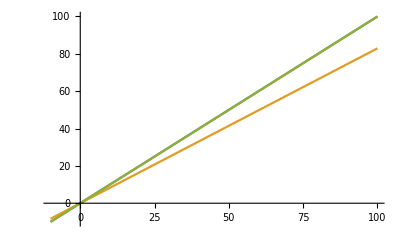
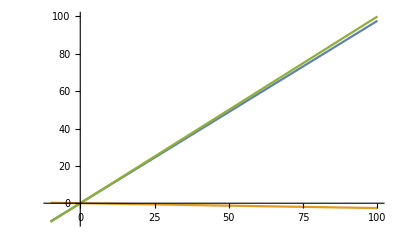
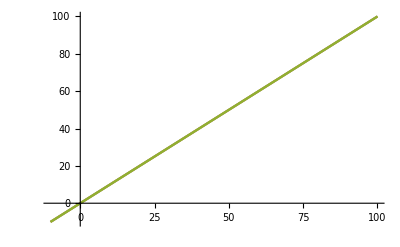
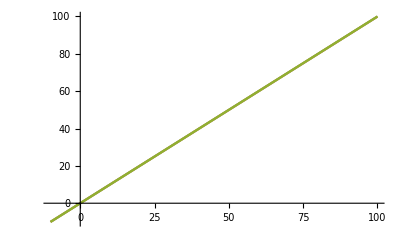
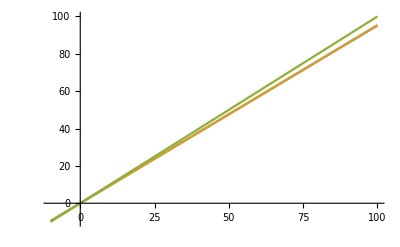
```mathematica
set4=Grid[{{" probel","1","2","3","4","5","6","7",8,9,10,11,12,13,14,15,16,17},{"step",  1.474770748346179*^-7 ,1.663300596111322*^-6 , 0.00001682338744689278 ,0.000016951129504751928,0.00017037925410167296,0.00016673843257936883,0.0016764754601306551,0.0165362078202515,0.03423438497026879,0.0634237208878754,0.08527722566220738,0.05124547904152914,0.04557517157169414,0.09557199804196258,0.10649483311156065,0.12209490218908951,0.18731979701339144,0.21645496343900403},{"a",0.9999999783789264, 0.9999977058630101 ,0.9997690012138877 ,0.9997937622978565,0.9769764976044127,0.9999902726058693,0.9993394874982948,0.9517364229632117,0.8506873992889905,0.5984771160820948,0.027018472337449556,0.16226130320245333,0.21151439582186968,0.20707098350945,0.2691889798131416,0.02309832782193066,-0.0076902284106143285},{"b",0.05285125940409576, 0.047203674933657805, 0.04683366536691023,0.8292884938435959,-0.026060380412454648,0.9999908598838421,0.9993725630563327,0.953668127576485,0.8454055390538759,0.6089946801312576,0.036339063760016665,0.18288842190906893,0.1887477075134105,0.21770131794401257,0.27935822879700567,0.017619885898523056,-0.004987200167593649},{"probel",-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{"probel",-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}},Frame->All]
```

probel | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 
step | 1.47477×10^-7 | 1.6633×10^-6 | 0.0000168234 | 0.0000169511 | 0.000170379 | 0.000166738 | 0.00167648 | 0.0165362 | 0.0342344 | 0.0634237 | 0.0852772 | 0.0512455 | 0.0455752 | 0.095572 | 0.106495 | 0.122095 | 0.18732 | 0.216455
a | 1. | 0.999998 | 0.999769 | 0.999794 | 0.976976 | 0.99999 | 0.999339 | 0.951736 | 0.850687 | 0.598477 | 0.0270185 | 0.162261 | 0.211514 | 0.207071 | 0.269189 | 0.0230983 | -0.00769023 | 
b | 0.0528513 | 0.0472037 | 0.0468337 | 0.829288 | -0.0260604 | 0.999991 | 0.999373 | 0.953668 | 0.845406 | 0.608995 | 0.0363391 | 0.182888 | 0.188748 | 0.217701 | 0.279358 | 0.0176199 | -0.0049872 | 
probel | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
probel | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |

Part::partd: Part specification set4⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::partd: Part specification set4⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of set4⟦1⟧ does not exist.

Part::partw: Part 3 of set4⟦1⟧⟦3⟧ does not exist.

Part::partw: Part 4 of set4⟦1⟧⟦3⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification set4⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::partd: Part specification set4⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 4 of set4⟦1⟧ does not exist.

Part::partw: Part 3 of set4⟦1⟧⟦4⟧ does not exist.

Part::partw: Part 4 of set4⟦1⟧⟦4⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{-3.43146×10^-36,6.52398×10^6},{-3.43146×10^-36,6.52398×10^6}}

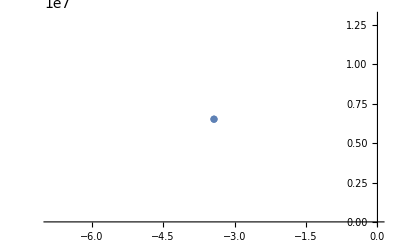

```mathematica
seta=Table[{set4[[1]][[2]][[i]],set4[[1]][[3]][[i]]},{i,2,18}];
setb=Table[{set4[[1]][[2]][[i]],set4[[1]][[4]][[i]]},{i,2,18}];
(*ListPlot[{seta,setb},PlotRange->All]*)
set1=Import["/Users/artemiyrr/Desktop/qwertyuiop1/a2 copy.csv"];
table= Import["/Users/artemiyrr/Desktop/qwertyuiop1/awertyuiop.csv"];
table
ListPlot[table]
```

```mathematica
set1=Import["/Users/artemiyrr/Desktop/qwertyuiop1/a2 copy.csv"];

N[2^(2/3)/7]




a=1;
b=-2;
c=0;
d=1;
MatrixForm[({{a, c}, {b, d}}).({{1, 2}, {2, 5}}).({{a, b}, {c, d}})]
```

0.226772

(1 | 0
0 | 1)

```mathematica
({{a (a+2 c)+c (2 a+5 c), b (a+2 c)+(2 a+5 c) d}, {a (b+2 d)+c (2 b+5 d), b (b+2 d)+d (2 b+5 d)}})
```

{{a (a+2 c)+c (2 a+5 c),b (a+2 c)+(2 a+5 c) d},{a (b+2 d)+c (2 b+5 d),b (b+2 d)+d (2 b+5 d)}}

```mathematica
Simplify[b (a+2 c)+(2 a+5 c) d-a (b+2 d)+c (2 b+5 d)]
```

```mathematica
1430/(Binomial[16,2]*Binomial[14,2]*Binomial[12,2]*Binomial[10,2]*Binomial[8,2]*Binomial[6,2]*Binomial[4,2]*Binomial[4,2])
```

1/342921600

```mathematica
|
```

```mathematica
90*11*13
```

12870

```mathematica
Grid[{{" probel ",1,2},{"step",  "3*pow(10,-6)", " 5*pow(10,-6) "}}]
```

probel  | 1 | 2
step | 3*pow(10,-6) |  5*pow(10,-6)

```mathematica
Apart[(x+e)^3-x]
```

```mathematica
FourierTransform[Sin[t]/t,t,p]
```

1/2 √(π/2) (Sign[1-p]+Sign[1+p])

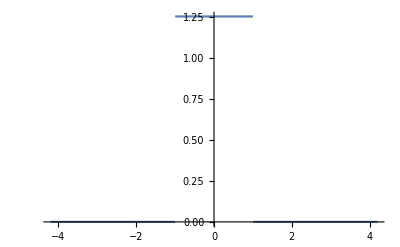

```mathematica
Plot[1/2 √(π/2) (Sign[1-p]+Sign[1+p]),{p,-4.2,4.2}]
```

```mathematica
CatalanNumber[3]
```

5

```mathematica
Factorial2[5]
```

15

```mathematica
N[49163.48/3600]
```

13.6565

```mathematica
0.99^3
```

0.970299

```mathematica
60*0.65
```

39.

```mathematica
Import["/Users/artemiyrr/Desktop/qwertyuiop1/a2 copy.txt]
```

```mathematica
MatrixForm[{{0,0,0},{0,0,0},{0,0,0}}]
```

```mathematica
({{0, 0, 0}, {1, 0, 0}, {0, 0, 0}}).({{0, 1, 0}, {0, 0, 0}, {0, 0, 0}})-({{0, 1, 0}, {0, 0, 0}, {0, 0, 0}}).({{0, 0, 0}, {1, 0, 0}, {0, 0, 0}})
```

{{-1,0,0},{0,1,0},{0,0,0}}

```mathematica
TraditionalForm[(Sum[aa[i],{i,1,Length[X]}]*Sum[bb[i],{i,1,Length[X]}])/(   Sqrt[Sum[(aa[i])^2,{i,1,Length[X]}]]*Sqrt[Sum[(bb[i])^2,{i,1,Length[X]}]])]
```

```mathematica
TraditionalForm[Sum[f[i],{i,1,k}]]
```

∑_(i=1)^k f(i)

```mathematica
Information[Indeterminate]
```

```mathematica
Norm[{3,4}]
```

5

```mathematica
Clear[x,y,z,a,b,c,q,w,e];
D[x^a*y^b*z^c,x]*z
```

a x^(-1+a) y^b z^(1+c)

```mathematica
ClearAll[n,m,k,c];
Construct[L,k];
CommuteL[n_,m_]:=(n-m)*L[n+m]+((c/12)n(n^2-1))(1-Sign[Abs[n+m-0]]);
CommuteL[L[3][[1]],L[2][[1]]];
CommuteL[CommuteL[L[3][[1]],L[2][[1]]][[1]],L[5][[1]]];
CommuteL[L[5][[1]],L[5][[1]]];
vector={L[1][[1]],L[-1][[1]],L[-3][[1]]};(*[Li*Ln,lj]*)
CommuteL2[vector_]:=Sum[Product[L[vector[[i]]]**CommuteL[vector[[i+1]],vector[[i+2]]],{i,1,Length[vector]-2}],{i,1,Length[vector]-2}];
CommuteL2[vector]
(*CommuteL1[q_,w_,e_]:=L[q]**CommuteL[w,e]+CommuteL[q,w]**L[e];
CommuteL1[L[1][[1]],L[2][[1]],L[2][[1]]]*)
(*L/:D[L[n_],ϵ,NonConstants->{L}]:=-n L[n-1]
T[expr_]:=D[expr,ϵ,NonConstants->{L}]
T[L[n]**L[m]]*)
```

L[1]**(2 L[-4])

```mathematica
NCAlg
```

```mathematica
comm[a_,b_,L_]:=Simplify[a[b[L]]-b[a[L]]];
comm[n,m,L]
```

```mathematica
Clear[f];
SetAttributes[f,HoldFirst];
f[s_Plus,b__]:=f[#,b]&/@List@@Hold[s][[1]]//Total
f[a+b+c,d,e]
```

f[a,d,e]+f[b,d,e]+f[c,d,e]

```mathematica
Integrate[1/Sqrt[a^2-x^2],x]
```

ArcTan[x/(√(a^2-x^2))]

```mathematica
Sin[ArcSin[x]];
FullSimplify[Sin[ArcTan[y0/x0]]*Cos[ArcTan[y/x]]-Cos[ArcTan[y0/x0]]*Sin[ArcTan[y/x]]]
```

(-x0 y+x y0)/(x x0 √(1+y^2/x^2) √(1+y0^2/x0^2))

x/(√(1-2 x^2))

```mathematica
a=1;b=1;ContourPlot3D[{{x^2-y^2-z^2==1},{a*x+b*y-z==0}},{x,0,10},{y,-10,10},{z,-10,10}]
```

-Graphics3D-

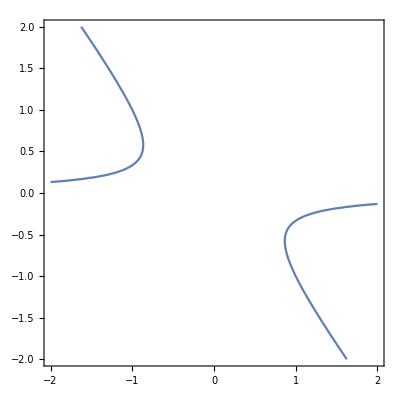

```mathematica
a=1;b=2;
ContourPlot[x^2+y^2-a^2*x^2-2a*b*x*y-b^2 y^2==1,{x,-2,2},{y,-2,2}]
```

```mathematica
Clear[a,b];
Solve[x^2+y^2-a^2*x^2-2a*b*x*y-b^2 y^2==1,y];
FullSimplify[(Cosh[x])^2-(Sinh[x])^2]
```

1

```mathematica
]
```

```mathematica
FullSimplify[D[Log[Cosh[θ+t]*Cosh[ϕ]-Cosh[θ+t]Sinh[ϕ]],{t,2}]]
```

Sech[t+θ]^2

```mathematica
}
```

```mathematica
FullSimplify[D[Log[x0-y0+a*Cosh[t]-b*Sinh[t]],{t,2}]]
```

((a-b) (a+b)+(x0-y0) (a Cosh[t]-b Sinh[t]))/(x0-y0+a Cosh[t]-b Sinh[t])^2

```mathematica
MatrixForm[KroneckerProduct[{{1,0},{0,0}},{{1,0},{0,0}}]]
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
FullSimplify[D[Sqrt[(x0+vx*t)^2+(y0+vy*t)^2],{t,2}]]
```

(vy x0-vx y0)^2/(((t vx+x0)^2+(t vy+y0)^2)^(3/2))

```mathematica
(vy x0-vx y0)^2/(((t vx+x0)^2+(t vy+y0)^2)^(3/2))
```

```mathematica
a=Import["/Users/artemiyrr/Desktop/qwertyuiop1/stars2.txt"];
a[1]
```

X,Y,Z
-35.7669,2.04261,0.0956439,0.543914
-34.0669,-53.2358,0.772673,0.630025
-29.4487,-71.118,0.861905,0.273544
-38.1971,81.9103,0.67693,0.328441
59.2….7002,389996,0.219718
22.4862,52.7531,389997,0.509846
0.786434,64.6502,389997,1.15915
5.48753,-49.5052,389999,0.221531
65.5923,5.52106,389999,0.0346254[1]
 |  |  |  |

```mathematica
aaaaaa={{-3.46913*10^-36,6.52398*10^6}->1,{1.58068*10^-32,6.52398*10^6}->2,{1.65371*10^-32,6.52398*10^6}->3,{1.38653*10^-32,6.52398*10^6}->4,{1.69634*10^-32,6.52398*10^6}->5,{1.48104*10^-32,6.52398*10^6}->6,{1.21876*10^-32,
6.52398*10^6}->7};

ListPlot[aaaaaa]
```

-Graphics-

```mathematica
aaaaaa1={{-3.46913*10^-36,6.52398*10^6}->1,{-3.43146*10^-36,6.52398*10^6}->2,{-3.39381*10^-36,6.52398*10^6}->3};
ListPlot[aaaaaa1]
```

-Graphics-

```mathematica
Series[Exp[-Pi*EllipticK[1-z]/EllipticK[z]],{z,0,4}]
```

z/16+z^2/32+(21 z^3)/1024+(31 z^4)/2048+O[z]^5

```mathematica
1024/(16)
```

64

```mathematica
FullSimplify[D[(1+2 x^2)/(1+x^2),x]]
```

(2 x)/((1+x^2)^2)

```mathematica
MatrixForm[IdentityMatrix[4]];
```

```mathematica
({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})
```

```mathematica
Print["L1 : ", MatrixForm[  ({{p, 0, q*w, 0}, {0, p, 0, q*w}, {q*w, 0, -p, 0}, {0, q*w, 0, -p}})]];Print["L2 : ", MatrixForm[ ({{p, w*q, 0, 0}, {w*q, -p, 0, 0}, {0, 0, p, w*q}, {0, 0, w*q, -p}} )]];
Print["r12 : ",MatrixForm[({{r1111, r1112, r1211, r1212}, {r1121, r1122, r1221, r1222}, {r2111, r2112, r2211, r2212}, {r2121, r2122, r2221, r2222}})]];
Print["r21 : ",MatrixForm[({{r1111, r1211, r1112, r1212}, {r2111, r2211, r2112, r2212}, {r1121, r1221, r1122, r1222}, {r2121, r2221, r2122, r2222}})]];
Print["{L1 ; L2} : " ,MatrixForm[ {{0,-w,w,0},{-w,0,0,-w},{w,0,0,w},{0,-w,w,0}}]]
MatrixForm[FullSimplify[({{r1111, r1112, r1211, r1212}, {r1121, r1122, r1221, r1222}, {r2111, r2112, r2211, r2212}, {r2121, r2122, r2221, r2222}}).({{p, 0, q*w, 0}, {0, p, 0, q*w}, {q*w, 0, -p, 0}, {0, q*w, 0, -p}})-({{p, 0, q*w, 0}, {0, p, 0, q*w}, {q*w, 0, -p, 0}, {0, q*w, 0, -p}}).({{r1111, r1112, r1211, r1212}, {r1121, r1122, r1221, r1222}, {r2111, r2112, r2211, r2212}, {r2121, r2122, r2221, r2222}})-(({{r1111, r1211, r1112, r1212}, {r2111, r2211, r2112, r2212}, {r1121, r1221, r1122, r1222}, {r2121, r2221, r2122, r2222}}).({{p, w*q, 0, 0}, {w*q, -p, 0, 0}, {0, 0, p, w*q}, {0, 0, w*q, -p}})-({{p, w*q, 0, 0}, {w*q, -p, 0, 0}, {0, 0, p, w*q}, {0, 0, w*q, -p}}).({{r1111, r1211, r1112, r1212}, {r2111, r2211, r2112, r2212}, {r1121, r1221, r1122, r1222}, {r2121, r2221, r2122, r2222}}))]]
```

L1 : (p | 0 | q w | 0
0 | p | 0 | q w
q w | 0 | -p | 0
0 | q w | 0 | -p)

L2 : (p | q w | 0 | 0
q w | -p | 0 | 0
0 | 0 | p | q w
0 | 0 | q w | -p)

r12 : (r1111 | r1112 | r1211 | r1212
r1121 | r1122 | r1221 | r1222
r2111 | r2112 | r2211 | r2212
r2121 | r2122 | r2221 | r2222)

r21 : (r1111 | r1211 | r1112 | r1212
r2111 | r2211 | r2112 | r2212
r1121 | r1221 | r1122 | r1222
r2121 | r2221 | r2122 | r2222)

{L1 ; L2} : (0 | -w | w | 0
-w | 0 | 0 | -w
w | 0 | 0 | w
0 | -w | w | 0)

(q w ((1+p) (r1211-r2111)+q (r1221-r2121) w) | -2 p^2 r1211+p q (r1111-2 r1221-r2211) w+q w (r1212-r2112+q (r1121-r2221) w) | -2 p r1211+p q (r1212-r2112) w+q w (r1111-r2211+q (r1222-r2122) w) | -2 p (1+p) r1212+q (r1112+p r1112-2 p r1222-(1+p) r2212) w+q^2 (r1122-r2222) w^2
2 p^2 r2111+p q (-r1111+2 r2121+r2211) w+q w (r1221-r2121+q (-r1121+r2221) w) | q w (r1222+p (-r1211+r2111)-r2122+q (-r1221+r2121) w) | -2 p r1221+2 p^2 r2112+p q (-r1112+2 r2122+r2212) w+q w (r1121-r2221+q (-r1122+r2222) w) | -2 p r1222+p q (-r1212+r2112) w+q w (r1122-r2222+q (-r1222+r2122) w)
2 p r2111+p q (-r1221+r2121) w+q w (-r1111+r2211+q (r1211-r2111) w) | 2 p^2 r1221+2 p r2112+p q (-r1121-2 r1211+r2221) w+q w (-r1112+r2212+q (r1111-r2211) w) | q w (-r1211+r2111+p (-r1222+r2122)+q (r1212-r2112) w) | 2 p^2 r1222+p q (-r1122-2 r1212+r2222) w+q w (-r1212+r2112+q (r1112-r2212) w)
2 p r2121-2 p^2 r2121+p q (r1121+2 r2111-r2221) w+q w (-r1121+r2221+q (-r1111+r2211) w) | 2 p r2122+p q (r1221-r2121) w+q w (-r1122+r2222+q (-r1211+r2111) w) | -2 p^2 r2122+p q (r1122+2 r2112-r2222) w+q w (-r1221+r2121+q (-r1112+r2212) w) | -q w (r1222-p r1222+(-1+p) r2122+q (r1212-r2112) w))

```mathematica
Solve[({{q *w *((1+p) (r1211-r2111)+q *(r1221-r2121)* w), -2 p^2 r1211+p *q (r1111-2 r1221-r2211) w+q w (r1212-r2112+q (r1121-r2221) w), -2 p r1211+p q (r1212-r2112) w+q w (r1111-r2211+q (r1222-r2122) w), -2 p (1+p) r1212+q (r1112+p r1112-2 p r1222-(1+p) r2212) w+q^2 (r1122-r2222) w^2}, {2 *p^2 *r2111+p* q *(-r1111+2 r2121+r2211)* w+q* w* (r1221-r2121+q *(-r1121+r2221)* w), q w (r1222+p (-r1211+r2111)-r2122+q (-r1221+r2121) w), -2 p r1221+2 p^2 r2112+p q (-r1112+2 r2122+r2212) w+q w (r1121-r2221+q (-r1122+r2222) w), -2 p r1222+p q (-r1212+r2112) w+q w (r1122-r2222+q (-r1222+r2122) w)}, {2* p *r2111+p *q *(-r1221+r2121)* w+q *w* (-r1111+r2211+q *(r1211-r2111)* w), 2 p^2 r1221+2 p r2112+p q (-r1121-2 r1211+r2221) w+q w (-r1112+r2212+q (r1111-r2211) w), q w (-r1211+r2111+p (-r1222+r2122)+q (r1212-r2112) w), 2 p^2 r1222+p q (-r1122-2 r1212+r2222) w+q w (-r1212+r2112+q (r1112-r2212) w)}, {2* p *r2121-2* p^2*r2121+p *q *(r1121+2 *r2111-r2221)* w+q* w *(-r1121+r2221+q *(-r1111+r2211)* w), 2 p r2122+p q (r1221-r2121) w+q w (-r1122+r2222+q (-r1211+r2111) w), -2 p^2 r2122+p q (r1122+2 r2112-r2222) w+q w (-r1221+r2121+q (-r1112+r2212) w), -q w (r1222-p r1222+(-1+p) r2122+q (r1212-r2112) w)}})==({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}),{r1111,r1211,r1112,r1212,r2111,r2211,r2212,r1121,r1221,r1122,r1222,r2121,r2221,r2122,r2222,r2112}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{r2111→r1211,r2211→r1111-(2 p r1211)/(q w),r2212→r1112-(2 p r1212)/(q w),r2121→r1221,r2221→r1121-(2 p r1221)/(q w),r2122→r1222,r2222→r1122-(2 p r1222)/(q w),r2112→r1212}}

```mathematica
Solve[{{a ,b z q},{c z,d}}==q IdentityMatrix[2],{a,b,c,d}]
```

{{a→q/(r w),b→0,c→0,d→q}}

```mathematica
MatrixForm[KroneckerProduct[IdentityMatrix[2],{{p,wq},{wq,-p}}]]
```

(p | wq | 0 | 0
wq | -p | 0 | 0
0 | 0 | p | wq
0 | 0 | wq | -p)

```mathematica
MatrixForm[PauliMatrix[1].PauliMatrix[1]]
```

(1 | 0
0 | 1)

```mathematica
({{0, -2}, {2, 0}});
MatrixForm[flpha({{p, q w, 0, 0}, {q w, -p, 0, 0}, {0, 0, p, q w}, {0, 0, q w, -p}})]
```

(0 | 0 | -2 ⅈ | 0
0 | 0 | 0 | 2 ⅈ
-2 ⅈ | 0 | 0 | 0
0 | 2 ⅈ | 0 | 0)

```mathematica
MatrixForm[KroneckerProduct[PauliMatrix[1],PauliMatrix[3]]-KroneckerProduct[PauliMatrix[3],PauliMatrix[1]]]
```

(0 | -1 | 1 | 0
-1 | 0 | 0 | -1
1 | 0 | 0 | 1
0 | -1 | 1 | 0)

```mathematica
Clear[a];Integrate[Exp[-I*t*x]*(1/2+Cos[t]+I*Sin[t]/6),{t,-Infinity,Infinity},Assumptions->{x∈Reals,σ∈Reals,a∈Reals,σ>0}]
```

Integrate::idiv: Integral of 1/2 ⅇ^(-ⅈ t x)+ⅇ^(-ⅈ t x) Cos[t]+1/6 ⅈ ⅇ^(-ⅈ t x) Sin[t] does not converge on {-∞,∞}.

Integrate[ⅇ^(-ⅈ t x) (1/2+Cos[t]+1/6 ⅈ Sin[t]),{t,-∞,∞},Assumptions→{x∈ℝ,σ∈ℝ,a∈ℝ,σ>0}]

```mathematica
TrigToExp[I*Sin[t]]
```

-1/2 ⅇ^(-ⅈ t)+ⅇ^(ⅈ t)/2

```mathematica
Simplify[1/2 ⅈ ⅇ^(-ⅈ t)-1/2 ⅈ ⅇ^(ⅈ t)]
```

```mathematica
FourierTransform[1/(2-Exp[-I*t]),t,x]
```

FourierTransform::argm: FourierTransform called with 2 arguments; 3 or more arguments are expected.

FourierTransform[1/(2-ⅇ^(-ⅈ t)),{t,x}]

```mathematica
1+5/6+7/6
```

3

```mathematica
Simplify[2/((-ⅈ+t) (ⅈ+t))]
```

2/(1+t^2)

```mathematica
Integrate[DiracDelta[-1-y],{y,-Infinity,-1}]
```

1-HeavisideTheta[0]

```mathematica
Sum[k,{k,0,n},Assumptions->{n∈Integers,n>0}]
```

1/2 n (1+n)

```mathematica
Solve[{{a,b,c},{x,y,z},{s,d,e}}.{{a1,b1,c1},{x1,y1,z1},{s1,d1,e1}}-{{a1,b1,c1},{x1,y1,z1},{s1,d1,e1}}.{{a,b,c},{x,y,z},{s,d,e}}==0,{a1,b1,c1,x1,y1,z1,s1,d1,e1}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x1→-(c1 (-c d x+b s z))/(c^2 d-b c e+b c y-b^2 z)-(b1 (c e x-c x y-c s z+b x z))/(c^2 d-b c e+b c y-b^2 z),y1→a1-(c1 (a c d-b c s-c d y+b d z))/(c^2 d-b c e+b c y-b^2 z)-(b1 (-a c e+c^2 s+a c y+c e y-c y^2-a b z-c d z+b y z))/(c^2 d-b c e+b c y-b^2 z),z1→-(c1 (b c x-a b z-c d z+b e z))/(c^2 d-b c e+b c y-b^2 z)-(b1 (-c^2 x+a c z-c y z+b z^2))/(c^2 d-b c e+b c y-b^2 z),s1→-(c1 (-c d s+b e s+b d x-b s y))/(c^2 d-b c e+b c y-b^2 z)-(b1 (-c d x+b s z))/(c^2 d-b c e+b c y-b^2 z),d1→-(c1 (-a b d-c d^2+b d e+b^2 s))/(c^2 d-b c e+b c y-b^2 z)-(b1 (a c d-b c s-c d y+b d z))/(c^2 d-b c e+b c y-b^2 z),e1→a1-(c1 (a c d-a b e-c d e+b e^2-b^2 x+a b y-b e y+b d z))/(c^2 d-b c e+b c y-b^2 z)-(b1 (b c x-a b z-c d z+b e z))/(c^2 d-b c e+b c y-b^2 z)}}

```mathematica
a=KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]+KroneckerProduct[PauliMatrix[2],PauliMatrix[2]];
b=a.L2-L2.a;
L1=({{p, 0, q*w, 0}, {0, p, 0, q*w}, {q*w, 0, -p, 0}, {0, q*w, 0, -p}});
MatrixForm[b/(8*I*p*q)];
Print[" r12 :" ,MatrixForm[(1/(2*I*q))*KroneckerProduct[PauliMatrix[2],PauliMatrix[1]]]];
Print ["r12 из лекции : " , MatrixForm[(w/(2*p))*I*KroneckerProduct[PauliMatrix[2],PauliMatrix[3]]]];
Print[" r 12 + a:",MatrixForm[(-I*1/(2*I*q))*KroneckerProduct[PauliMatrix[2],PauliMatrix[1]]+b/(8*I*p*q)]];
```

r12 :(0 | 0 | 0 | -1/(2 q)
0 | 0 | -1/(2 q) | 0
0 | 1/(2 q) | 0 | 0
1/(2 q) | 0 | 0 | 0)

r12 из лекции : (0 | 0 | w/(2 p) | 0
0 | 0 | 0 | -w/(2 p)
-w/(2 p) | 0 | 0 | 0
0 | w/(2 p) | 0 | 0)

r 12 + a:(0 | 0 | (ⅈ w)/(2 p) | 0
0 | 0 | 0 | -(ⅈ w)/(2 p)
-(ⅈ w)/(2 p) | 0 | 0 | 0
0 | (ⅈ w)/(2 p) | 0 | 0)

```mathematica
MatrixForm[(w/(2*p))*KroneckerProduct[PauliMatrix[2],PauliMatrix[3]]-({{0, 0, -(ⅈ w)/(2 p), ⅈ/(2 q)}, {0, 0, ⅈ/(2 q), (ⅈ w)/(2 p)}, {(ⅈ w)/(2 p), -ⅈ/(2 q), 0, 0}, {-ⅈ/(2 q), -(ⅈ w)/(2 p), 0, 0}})]
```

(0 | 0 | 0 | -ⅈ/(2 q)
0 | 0 | -ⅈ/(2 q) | 0
0 | ⅈ/(2 q) | 0 | 0
ⅈ/(2 q) | 0 | 0 | 0)

```mathematica
MatrixForm[%908]
```

(p-2 ⅈ q w | 2 ⅈ p | -(ⅈ w)/(2 p)+q w | 1/(2 q)-2 ⅈ q w
2 ⅈ p | p+2 ⅈ q w | 1/(2 q)+2 ⅈ q w | (ⅈ w)/(2 p)+q w
(ⅈ w)/(2 p)+q w | -1/(2 q)+2 ⅈ q w | -p+2 ⅈ q w | -2 ⅈ p
-1/(2 q)-2 ⅈ q w | -(ⅈ w)/(2 p)+q w | -2 ⅈ p | -p-2 ⅈ q w)

```mathematica
MatrixForm[KroneckerProduct[PauliMatrix[2],PauliMatrix[3]]]
```

(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)

```mathematica
TrigToExp[InverseFourierTransform[Exp[-t^2]*(Cos[t]),t,y]]
```

(ⅇ^(-1/4 (-1+y)^2))/(2 √2)+(ⅇ^(-1/4 (1+y)^2))/(2 √2)

```mathematica
FullSimplify[(ⅇ^(-1/4-y^2/4) Cosh[y/2])/(√2)-(2)(Exp[-(1-y)^2/4]+Exp[-(1+y)^2/4])]
```

1/4 (-8+√2) ⅇ^(-1/4 (1+y)^2) (1+ⅇ^y)

```mathematica
TrigToExp[Cosh[x]]
```

ⅇ^-x/2+ⅇ^x/2

```mathematica
Integrate[(1/(4*Sqrt[Pi]))*(Exp[-(1-y)^2/4]+Exp[-(1+y)^2/4]),{y,-Infinity,x}]
```

1/4 (2+Erf[1/2 (-1+x)]+Erf[(1+x)/2])

```mathematica
MatrixForm[{{0.4,0.6,0.2},{0.3,0.2,0.4},{0.3,0.2,0.4}}]
```

```mathematica
MatrixForm[({{0.4, 0.2, 0.4}, {0.3, 0.6, 0.4}, {0.3, 0.2, 0.2}}).({{0.2}, {0.3}, {0.5}})]
```

(0.34
0.44
0.22)

```mathematica
MatrixForm[{0.2,0.3,0.5}]
```

(0.2
0.3
0.5)

```mathematica
{{0.2, □}, {0.3, □}, {0.5, □}}
```

```mathematica
TableForm[{{0.6859943405700353,0.5144957554275266,0.5144957554275266},{-0.8164965809277261,0.408248287897418,0.40824829303030796},{0.8164965809277261,-0.40824829303030824,-0.4082482878974179}}]
```

0.685994 | 0.514496 | 0.514496
-0.816497 | 0.408248 | 0.408248
0.816497 | -0.408248 | -0.408248

```mathematica
Clear[a];
JordanDecomposition[{{1-a,a},{b,1-b}}];
Map[MatrixForm,%]
```

{(1 | -a/b
1 | 1),(1 | 0
0 | 1-a-b)}

```mathematica
Simplify[MatrixForm[({{1, -a/b}, {1, 1}}).({{1, 0}, {0, (1-(a+b))^n}}).Inverse[({{1, -a/b}, {1, 1}})]]]
```

```mathematica
Limit[({{(a (1-a-b)^n+b)/(a+b), (a-a (1-a-b)^n)/(a+b)}, {(b-(1-a-b)^n b)/(a+b), (a+(1-a-b)^n b)/(a+b)}}),n->Infinity,Assumptions->{a>=0,a<=1,b>=0,b<=1}]
```

{{ConditionalExpression[b/(a+b), Log[1-a-b]<0],ConditionalExpression[a/(a+b), Log[1-a-b]<0]},{ConditionalExpression[b/(a+b), Log[1-a-b]<0],ConditionalExpression[a/(a+b), Log[1-a-b]<0]}}

```mathematica
MatrixForm[Limit[({{1, -1}, {1, 1}}).({{1, 0}, {0, (1-2 a)^n}}).Inverse[({{1, -1}, {1, 1}})],n->Infinity,Assumptions->{a ∈ Reals,a>=0}]]
```

{{1,0},{0,1-2 a}}

ConditionalExpression[1/2, Log[1-2 a]<0] | ConditionalExpression[1/2, Log[1-2 a]<0]
ConditionalExpression[1/2, Log[1-2 a]<0] | ConditionalExpression[1/2, Log[1-2 a]<0]

```mathematica
Limit[(1/2)(1-(1-2*a)^n),n->Infinity,Assumptions->{a==1}]
```

1/2 (1-ⅇ^(2 ⅈ Interval[{0,π}]))

```mathematica
MatrixForm[Limit[MatrixPower[({{1-a, a}, {b, 1-b}}),n],n->Infinity,Assumptions->{a>=0,b<=1}]]
```

(ConditionalExpression[b/(a+b), Log[1-a-b]<0] | ConditionalExpression[a/(a+b), Log[1-a-b]<0]
ConditionalExpression[b/(a+b), Log[1-a-b]<0] | ConditionalExpression[a/(a+b), Log[1-a-b]<0])

```mathematica
Integrate[2*Exp[-(x)^2/(2)],{x,0,Infinity}]/Sqrt[(2Pi)]
```

1

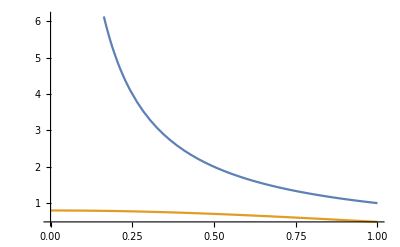

```mathematica
Plot[{1/x,Sqrt[2/Pi]*Exp[-x^2/2]},{x,0,1}]
```

```mathematica
Sqrt[2/Pi]
```

√(2/π)

```mathematica
N[√(2/π)]
```

0.797885

```mathematica
N[(105*3+90*4+60*4+90*4+135*4+60*3+105*3+195*3+90*3+90*4+105*3+90*4+105*3+135*2+150*4+45*4+150*3+90*4+60*3+90*4+195*4+450+720+540+180+540+450+270+360+450+720+540+600+540+300+360+360+450+405+390+420+270+720+300+600+315+405+300+270+315+135+180)/(150+240+180+45+135+150+90+180+150+240+135+150+180+150+90+105+90+60+90+135+60+105+195+90+90+105+90+105+135+180+150+135+195+105+90+180+150+150+105+135+150+90+105+45+90+150+45+150+90+60+90+195)]
```

3.13501

```mathematica
-50+15/1.03+(3/(1.03)^2)*(Sum[(1/1.03)^n,{n,0,Infinity}])
```

61.6505

```mathematica
Sum[(4/5)^n,{n,0,Infinity}]
```

5

```mathematica
N[5/4]
```

1.25

```mathematica
Integrate[Exp[-x^2/2],{x,0,Infinity}]
```

√(π/2)

```mathematica
FullSimplify[D[ArcTan[Sqrt[s/(t-s)]],t]]
```

-(√(s/(-s+t)))/(2 t)

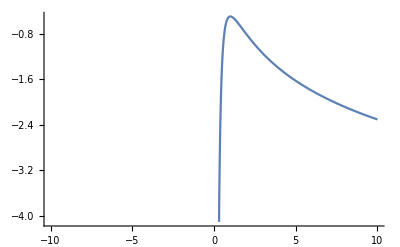

```mathematica
Plot[-Log[x]-1/(2*x^2),{x,-10,10}]
```

```mathematica
Limit[Simplify[TrigToExp[Coth[(h*w) /(2*T)]]],T->0]
```

ConditionalExpression[Indeterminate, h w>0]

```mathematica
Limit[(1+ⅇ^((h w)/T))/(-1+ⅇ^((h w)/T)),T->Infinity]
```

DirectedInfinity[1/(Sign[h] Sign[w])]

```mathematica
Integrate[z/(Exp[z^2]-1),{z,-Infinity,Infinity}]
```

Integrate::idiv: Integral of z/(-1+ⅇ^(z^2)) does not converge on {-∞,∞}.

```mathematica
∫_(-∞)^∞ z/(-1+ⅇ^(z^2))ⅆz
```

```mathematica
Series[1/(1/x-1),{x,0,2}]
```

x+x^2+O[x]^3

```mathematica
D[x*Log[x],{x,2}]
```

1/x

```mathematica
(*A={{a,b,c,α*Subscript[u, 1]},{d,e,f,β*Subscript[u, 2]},{g,h,i,γ*Subscript[u, 3]},{ϵ*v^("1"),ξ*v^("2"),θ*v^("3"),z}};B={{a1,b1,c1,Subscript[α, 1]*Subscript[u, 1]},{d1,e1,f1,Subscript[β, 1]*Subscript[u, 2]},{g1,h1,i1,Subscript[γ, 1]*Subscript[u, 3]},{Subscript[ϵ, 1]*v^("1"),Subscript[ξ, 1]*v^("2"),Subscript[θ, 1]*v^("3"),z1}};*)
(*A={{a,b,c,0},{d,e,f,0},{g,h,i,0},{0,0,0,z}};*)A={{0,0,0,α*Subscript[u, 1]},{0,0,0,β*Subscript[u, 2]},{0,0,0,γ*Subscript[u, 3]},{0,0,0,0}};
Clear[a];
(*A={{a,b,c,0},{d,e,f,0},{g,h,i,0},{0,0,0,z}};*)
B={{0,0,0,0},{0,0,0,0},{0,0,0,0},{ϵ*v^("1"),ξ*v^("2"),θ*v^("3"),0}};
X={{a1,0,0},{0,b1,0},{0,0,-a1-b1}};
Y = {{a2,b2,c2},{d2,e2,f2},{g2,i2,-a2-e2}};
h1={{1,0,0},{0,-1,0},{0,0,0}};
h2={{1,0,0},{0,0,0},{0,0,-1}};
B1={{a1,b1,c1},{d1,e1,f1},{g1,h1,i1}};
B2={{a1,b1,c1,0},{d1,e1,f1,0},{g1,h1,i1,0},{0,0,0,0}};
a=3;
b=1;
Clear[z];
v={x,y,z};
L=Sign[a-b]*{{ 1/3 (-α ϵ-γ θ-β ξ),0,0,0},{0,1/3 (-α ϵ-γ θ-β ξ),0,0},{0,0,1/3 (-α ϵ-γ θ-β ξ),0},{0,0,0,(α ϵ+γ θ+β ξ)}};
MatrixForm[X];
MatrixForm[h1.Y -Y.h1]==MatrixForm[Y];
MatrixForm[h2.Y -Y.h2]==MatrixForm[Y];
MatrixForm[h2.v]
MatrixForm[A.B-B.A+L];
MatrixForm[Transpose[{ϵ*v^("1"),ξ*v^("2"),θ*v^("3")}].A1];
MatrixForm[A1.{Subscript[α, 1]*Subscript[u, 1],Subscript[β, 1]*Subscript[u, 2],Subscript[γ, 1]*Subscript[u, 3]}];
FullSimplify[MatrixForm[X.Y-Y.X]];
TeXForm[L];
```

(x
0
-z)

Dot::rect: Nonrectangular tensor encountered.

```mathematica
Eigensystem[{{a1,0,0},{0,b1,0},{0,0,-a1-b1}}]
```

{{a1,-a1-b1,b1},{{1,0,0},{0,0,1},{0,1,0}}}

{a1,-a1-b1,b1}

```mathematica
MatrixForm[TensorProduct[{α*Subscript[u, 1],β*Subscript[u, 2],γ*Subscript[u, 3]},Transpose[{ϵ*v^("1"),ξ*v^("2"),θ*v^("3")}]]-1*IdentityMatrix[3]*(1/3)*(ϵ*α+ξ*β+θ*γ)]
```

(1/3 (-α ϵ-γ θ-β ξ)+v^1 α ϵ u_1 | v^2 α ξ u_1 | v^3 α θ u_1
v^1 β ϵ u_2 | 1/3 (-α ϵ-γ θ-β ξ)+v^2 β ξ u_2 | v^3 β θ u_2
v^1 γ ϵ u_3 | v^2 γ ξ u_3 | 1/3 (-α ϵ-γ θ-β ξ)+v^3 γ θ u_3)

```mathematica
MatrixForm[{a,b}.IdentityMatrix[2]]
```

(a
b)

```mathematica
TeXForm[({{a v^("1") ϵ+g v^("3") θ+d v^("2") ξ}, {b v^("1") ϵ+h v^("3") θ+e v^("2") ξ}, {c v^("1") ϵ+i v^("3") θ+f v^("2") ξ}})]
```

\left\{a \epsilon  v^1+d \xi  v^2+g \theta  v^3,b \epsilon  v^1+e \xi  v^2+h \theta 
   v^3,c \epsilon  v^1+f \xi  v^2+\theta  i v^3\right\}

```mathematica
ArcCos[-1/2]
```

```mathematica
Sin[(2 π)/3]
```

(√3)/2

```mathematica
Clear[a,b,h1,z,l,c];
y1=0;
y2=0;
y3=0;
Sx={{1,0,0},{0,-1/2,-Sqrt[3]/2},{0,Sqrt[3]/2,-1/2}};
Sy={{-1/2,0,(√3)/2},{0,1,0},{-(√3)/2,0,-1/2}};
A={{0,0,0,0,-2 α,-2 β,-2 γ},{α,0,0,0,0,0,0},{β,0,0,0,0,0,0},{γ,0,0,0,0,0,0},{0,0,-γ,β,0,0,0},{0,γ,0,-α,0,0,0},{0,-β,α,0,0,0,0}};
B={{0,-2 ϵ,-2 ξ,-2 θ,0,0,0},{0,0,0,0,0,-θ,ξ},{0,0,0,0,θ,0,-ϵ},{0,0,0,0,-ξ,ϵ,0},{ϵ,0,0,0,0,0,0},{ξ,0,0,0,0,0,0},{θ,0,0,0,0,0,0}};
A1={{a,b,c},{d,e,f},{g,h,i}};
B1=Transpose[{ϵ,ξ,θ}];
MatrixForm[-Transpose[B1]];
MatrixForm[B];
MatrixForm[(A.B-B.A)]
FullSimplify[MatrixForm[S.S1-S1.S]];
u={α,β,γ};
v=Transpose[{ϵ,ξ,θ}];
v1=v.Sx;
v2=v.Sy;
Solve[α*v1+β*v2+γ*v==0,{α,β,γ}];
TeXForm[MatrixForm[Sy]];
MatrixForm[Simplify[(TensorProduct[u,v]-1/3IdentityMatrix[3]*(α*ϵ+β*ξ+γ*θ))]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2 α ϵ+γ θ+β ξ | -3 α ξ | -3 α θ | 0 | 0 | 0
0 | -3 β ϵ | α ϵ+γ θ-2 β ξ | -3 β θ | 0 | 0 | 0
0 | -3 γ ϵ | -3 γ ξ | α ϵ-2 γ θ+β ξ | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 α ϵ-γ θ-β ξ | 3 β ϵ | 3 γ ϵ
0 | 0 | 0 | 0 | 3 α ξ | -α ϵ-γ θ+2 β ξ | 3 γ ξ
0 | 0 | 0 | 0 | 3 α θ | 3 β θ | -α ϵ+2 γ θ-β ξ)

(1/3 (2 α ϵ-γ θ-β ξ) | α ξ | α θ
β ϵ | 1/3 (-α ϵ-γ θ+2 β ξ) | β θ
γ ϵ | γ ξ | 1/3 (-α ϵ+2 γ θ-β ξ))

```mathematica
TeXForm[({{0, -2 a ϵ-2 g θ-2 d ξ, -2 b ϵ-2 h θ-2 e ξ, -2 c ϵ-2 i θ-2 f ξ, 0, 0, 0}, {0, 0, 0, 0, 2 b θ, -c ϵ+a θ+e θ-f ξ, b ϵ+h θ-a ξ-i ξ}, {0, 0, 0, 0, c ϵ+a θ+e θ+f ξ, 2 d θ, e ϵ+i ϵ+g θ-d ξ}, {0, 0, 0, 0, -b ϵ+h θ+a ξ+i ξ, -e ϵ-i ϵ+g θ+d ξ, 0}, {a ϵ+g θ+d ξ, 0, 0, 0, 0, 0, 0}, {b ϵ+h θ+e ξ, 0, 0, 0, 0, 0, 0}, {c ϵ+i θ+f ξ, 0, 0, 0, 0, 0, 0}})]
```

\left(
\begin{array}{ccccccc}
 0 & -2 a \epsilon -2 d \xi -2 g \theta  & -2 b \epsilon -2 e \xi -2 h \theta  & -2 c
   \epsilon -2 f \xi -2 \theta  i & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & 2 b \theta  & a \theta -c \epsilon +e \theta -f \xi  & -a \xi +b
   \epsilon +h \theta -i \xi  \\
 0 & 0 & 0 & 0 & a \theta +c \epsilon +e \theta +f \xi  & 2 d \theta  & -d \xi +e
   \epsilon +g \theta +i \epsilon  \\
 0 & 0 & 0 & 0 & a \xi -b \epsilon +h \theta +i \xi  & d \xi -e \epsilon +g \theta -i
   \epsilon  & 0 \\
 a \epsilon +d \xi +g \theta  & 0 & 0 & 0 & 0 & 0 & 0 \\
 b \epsilon +e \xi +h \theta  & 0 & 0 & 0 & 0 & 0 & 0 \\
 c \epsilon +f \xi +\theta  i & 0 & 0 & 0 & 0 & 0 & 0 \\
\end{array}
\right)

```mathematica
TeXForm[MatrixForm[B]]
```

\left(
\begin{array}{ccccccc}
 0 & -2 \epsilon  & -2 \xi  & -2 \theta  & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & 0 & -\theta  & \xi  \\
 0 & 0 & 0 & 0 & -\theta  & 0 & -\epsilon  \\
 0 & 0 & 0 & 0 & -\xi  & \epsilon  & 0 \\
 \epsilon  & 0 & 0 & 0 & 0 & 0 & 0 \\
 \xi  & 0 & 0 & 0 & 0 & 0 & 0 \\
 \theta  & 0 & 0 & 0 & 0 & 0 & 0 \\
\end{array}
\right)

```mathematica
MatrixForm[IdentityMatrix[7]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
({{0, 0, 0, 0, -2α, 0-2β, -2γ}, {α, 0, 0, 0, 0, 0, 0}, {β, 0, 0, 0, 0, 0, 0}, {γ, 0, 0, 0, 0, 0, 0}, {0, 0, -γ, β, 0, 0, 0}, {0, γ, 0, -α, 0, 0, 0}, {0, -β, α, 0, 0, 0, 0}})
```

{{0,0,0,0,-2 α,-2 β,-2 γ},{α,0,0,0,0,0,0},{β,0,0,0,0,0,0},{γ,0,0,0,0,0,0},{0,0,-γ,β,0,0,0},{0,γ,0,-α,0,0,0},{0,-β,α,0,0,0,0}}

```mathematica
({{-a1, -d1, -g1}, {-b1, -e1, -h1}, {-c1, -f1, -i1}})
```

{0,0,0}

```mathematica
{α,β,γ}/.{{α->0,β->0,γ->0}}
```

{{0,0,0}}

```mathematica
TeXForm[{{α->0,β->0,γ->0}}]
```

\{\{\alpha \to 0,\beta \to 0,\gamma \to 0\}\}

{}

```mathematica
|
```

```mathematica
TeXForm[ArcCos[-Sqrt[3/4]]]
```

\frac{5 \pi }{6}

```mathematica
Sin[5*Pi/6]
```

1/2

```mathematica
Import["/Users/artemiyrr/Desktop/ab.png]
```

```mathematica
2/3Pi-π/2
```

π/6

```mathematica
b1 d+b d1+e e1+c1 g+c g1+f h1+a (2 a1+h1)+h (a1+f1+h1)
```

```mathematica
TeXForm["α_1=λ_1-λ_2 ;
α_2= λ_3-λ_1;
α_3=λ_2"]
```

\alpha _1=\lambda _1-\lambda _2\text{ ;$\backslash $n}\alpha _2\text{= }\lambda
   _3-\lambda _{1\backslash }\text{;$\backslash $n}\alpha _3=\lambda _2

```mathematica
Sqrt[2*1]
```

√2

```mathematica
Clear[z];
FullSimplify[-(3/2)(D[f[g[z]],{z,2}]/D[f[g[z]],{z,1}])^2+D[f[g[z]],{z,3}]/D[f[g[z]],{z,1}]];
D[1/w'[x],{x,2}]
```

(2 w''[x]^2)/w'[x]^3-(w^(3)[x])/w'[x]^2

```mathematica
Simplify[(2 w''[x]^2)/w'[x]^3-(Derivative[3][w][x])/w'[x]^2]
```

(2 w''[x]^2-w'[x] w^(3)[x])/w'[x]^3

f'[g[z]] g'[z]

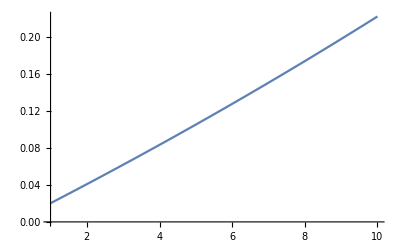

```mathematica
q=100;
Plot[2*x/(q-x),{x,1,10}]
```

```mathematica
A1={{6,12,6(Δ+2),0,(8+8*Δ+c)},{0,5,18+4*Δ+c/2,12(3*Δ+2),0},{5,6+2*Δ,0,0,-3},{0,4,2(5+2*Δ),0,6},{0,0,3,4*(3+2Δ),0}};
Det[A1]
MatrixForm[A1]
```

-528+408 c+120 c^2+4880 Δ+224 c Δ+80 c^2 Δ-5376 Δ^2+768 c Δ^2+1024 Δ^3

(6 | 12 | 6 (2+Δ) | 0 | 8+c+8 Δ
0 | 5 | 18+c/2+4 Δ | 12 (2+3 Δ) | 0
5 | 6+2 Δ | 0 | 0 | -3
0 | 4 | 2 (5+2 Δ) | 0 | 6
0 | 0 | 3 | 4 (3+2 Δ) | 0)

```mathematica
Solve[Det[({{6 (1+Δ), 3, 0}, {0, 2 Δ, 4}, {6 (1+3 Δ), 4+c/2+4 Δ, 5}})]==0,Δ]
```

{{Δ→1/6 (7-c-√(25-26 c+c^2))},{Δ→1/6 (7-c+√(25-26 c+c^2))}}

```mathematica
Simplify[1/12 (-24-12 c+84 Δ-12 c Δ-36 Δ^2)]
```

-2+7 Δ-3 Δ^2-c (1+Δ)

```mathematica
N1=200;
P=Sum[Binomial[N1,k]*(1/2)^N1*(20100+k),{k,0,N1}];
P
```

20200

```mathematica
(273+70)/7
```

49

```mathematica
49+7-1
```

55

```mathematica
160-(2*38+4)
```

80

```mathematica
1+1/64
```

65/64

```mathematica
(99/100+19/100)*2/8
```

59/200

```mathematica
P1=Sum[1*100/(3*2*1*(Binomial[k,3]))*(1/100),{k,3,102}]
```

2575/10302

```mathematica
N[P1]
```

```mathematica
16^2 Binomial[4,2]/Binomial[64,2]
```

16/21

```mathematica
16/21
```

16/21

```mathematica
|
```

```mathematica
7*8/63-16/21;
P4=8/63;
P6=32/63;
P5=16/63;
P3=4/63;
P2=2/63;
P1=1/63;
S=P1*1+P2*2+P3*3+P4*4+P5*5+P6*6;
S


(*Solve[1==P4+P5+P6+P3+P2+P1,P1]*)
```

107/21

```mathematica
4*3+2*3
```

18

```mathematica
19/200+8/(10*4)
```

59/200

```mathematica
S1=FullSimplify[Sum[1/(Binomial[m,3]*Factorial[3]),{m,3,102}]]
```

2575/10302

```mathematica
N[S1]
```

0.249951

```mathematica
Clear[a,z,y,x];
A={{a,b,c},{d,e,f},{h,i,j}};
a1={x,y,z};
a=0;
e=0;
j=0;
c=0;
f=0;
h=0;
i=0;
MatrixForm[A] 
MatrixForm[A.a1]
```

(0 | b | 0
d | 0 | 0
0 | 0 | 0)

(b y
d x
0)

```mathematica
B={{1,0},{0,-1}};
v={x,y};
Eigenvalues[B]
```

{-1,1}

```mathematica
Plot[2*(Cos[2*Pi*t]+I*Sin[2*Pi*t]),{t,0,1},PlotRange->All]
```

-Graphics-

```mathematica
ExpToTrig[Exp[I*x]]
```

Cos[x]+ⅈ Sin[x]

```mathematica
|
```

16/63

```mathematica
DSolve[-y^2*b'[y]+2*y*b[y]==2*y^2,b[y],y]
```

{{b[y]→2 y+y^2 C[1]}}

```mathematica
{{b[y]->1/2+y^2 C[1]}}
```

{{b[y]→1/2+y^2 C[1]}}